## Лабораторная работа №1

Лабораторная работа №1. Списки. Строки и текст.

### 1.1

1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[1,4]
```

{1,2,3,4}

2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[1,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

3. Используя функции Range и Reverse, создайте список {4, 3, 2, 1}

```mathematica
Reverse[Range[1,4]]
```

{4,3,2,1}

4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[1,50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

5. Используя функции Range, Reverse и Join, создайте список {1, 2, 3, 4, 4, 3, 2, 1}

```mathematica
Join[Range[1,4], Reverse[Range[1,4]]]
```

{1,2,3,4,4,3,2,1}

6. Нарисовать график списка чисел, которые возрастают от 1 до 100, а затем убывают от 100 
до 1

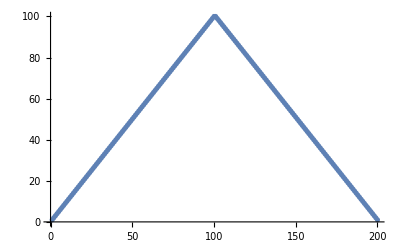

```mathematica
ListPlot[Join[Range[1,100], Reverse[Range[1,100]]]]
```

7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины, не превышающей число 10

```mathematica
Range[1,RandomInteger[10]]
```

{1,2}

8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]]

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

9. Найти простейшую форму для команды Join[{1, 2}, Join[{3, 4}, {5}]]

```mathematica
Range[1,5]
```

10. Найти простейшую форму для команды Join[Range[10], Join[Range[10], Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

11. Найти простейшую форму для команды Reverse[Join[Range[20], Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

### 1.2 Strings and Text

1. Присоедините две копии строки «Здравствуйте».

```mathematica
str = "Здравствуйте";
StringJoin[str, str]
```

ЗдравствуйтеЗдравствуйте

2. Создайте единую строку всего английского алфавита заглавными буквами.

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

3. Сгенерируйте строку английского алфавита в обратном порядке.

```mathematica
StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

4. Объедините 100 копий строки «ABCD»

```mathematica
StringRepeat["ABCD",100]
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]], 6]
```

abcdef

6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих
число букв (включая пробелы) равное номеру элемента.

```mathematica
str = "это о строках";
Column[Table[StringTake[str,i],{i,StringLength[str]}]]
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

{12,1,7,9,6}

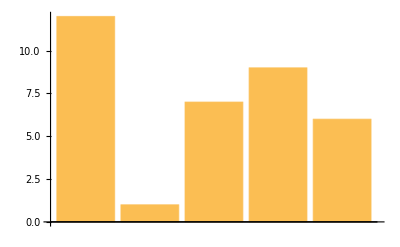

```mathematica
str = "Давным-давно, в далекой галактике, далеко";
strLength = StringLength[TextWords[str]]
BarChart[strLength]
```

8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
Max[StringLength[WordList[]]]
```

21

9. Используйте Length, чтобы найти длину русского алфавита.

```mathematica
Length[Alphabet["Russian"]]
```

33

10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
StringReverse[StringJoin[ToUpperCase[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

### 1.3

1. Используйте Range и чистую функцию для создания списка из квадратов первых 20 
натуральных чисел.

```mathematica
#^2 &/@ Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

2. Составьте список из результатов смешивания желтого, зеленого и синего цветов с красным
цветом.

```mathematica
Blend[{#, Red}] &/@ {Yellow, Green, Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

3. Создайте список столбцов в рамках, содержащих прописные и строчные версии каждой
буквы алфавита.

```mathematica
Framed[Column[{ToUpperCase[#], #}]] &/@ Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

4. Составьте список букв алфавита в случайных цветах в рамках, имеющих случайные цвета
фона.

```mathematica
Style[Framed[Style[#,RandomColor[]]],Background->RandomColor[]] &/@ Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

5. Напишите в более простой форме команду (#^2+1&)/@Range[10].

```mathematica
Range[10]^2 + 1
```

{2,5,10,17,26,37,50,65,82,101}

### 1.4

1. Составьте список результатов использования функции Blur до 10 раз, начиная с
растрированного размера 30 “X” (Используйте: Rasterize[Style]).

```mathematica
NestList[Blur,Rasterize["X", RasterSize->30], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

2. Начните с x, затем создайте список, использовав последовательно функцию Framed до 10 
раз, используя каждый раз случайный цвет фона.

```mathematica
NestList[Style[Framed[#],Background->RandomColor[]] &,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

3. Начните с размера 50 для “A”, затем создайте список вложенного применения Framed и случайного вращения 5 раз.

```mathematica
NestList[Rotate[Framed[#],RandomInteger[360]Degree] &, Rasterize["A",RasterSize->50],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-
#)&, начиная с 0.2.

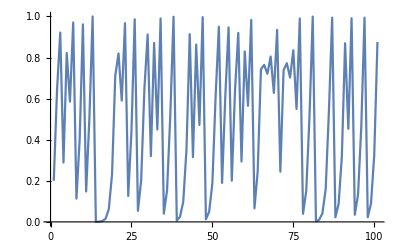

```mathematica
ListLinePlot[NestList[4 # (1-#)&,0.2,100]]
```

5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&, 
начиная с 1

```mathematica
Nest[1+1/#&,1,30]
```

2178309/1346269

6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.

```mathematica
NestList[3*#&,1/3,10]
```

{1/3,1,3,9,27,81,243,729,2187,6561,19683}

7. Составьте список результатов действия вложенной функции (метод Ньютона) (# + 2 / #) / 2 до
5 раз, начиная с 1.0, а затем вычтите 2 из всех результатов.

```mathematica
res = NestList[(#+2/#)/2&,1.0,5]
res - 2
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421}

{-1.,-0.5,-0.583333,-0.585784,-0.585786,-0.585786}

8. Создайте список из 5 степеней числа 2, т. е. 2 ^ 2 ^ 2 ... ^ 2 n раз, причем n меняется от 0 до 4.

```mathematica
Table[Nest[#^2&,2,i],{i,0,4}]
```

{2,4,16,256,65536}

### 1.5

1. Определите функцию f, которая вычисляет квадрат ее аргумента.

```mathematica
f[n_]:=n^2;
{f[2],f[3]}
```

{4,9}

2. Определите функцию poly, которая имеет целочисленное значение аргумента и создает
изображение оранжевого правильного многоугольника с числом сторон, равным значению
этого аргумента.

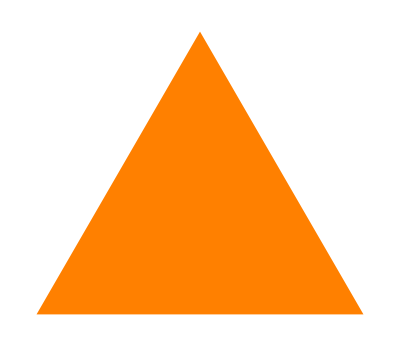

```mathematica
poly[n_Integer]:=Graphics[Style[RegularPolygon[n],Orange]];
poly[3]
```

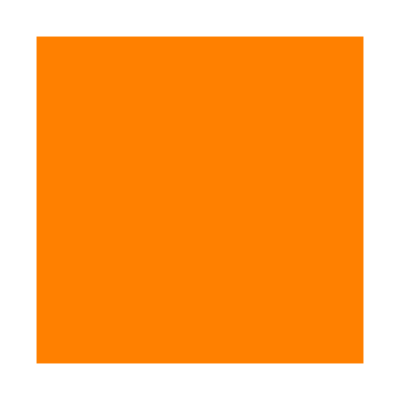

```mathematica
poly[4]
```

3. Определите функцию f, которая берет список из двух элементов и помещает их в обратном
порядке.

```mathematica
Clear[f];
f[{n_,m_}]:={m,n};
{f[{1,2}],f[{5,9}]}
```

{{2,1},{9,5}}

4. Определите функцию f, которая имеет два аргумента и дает результат в виде дроби, где
числитель равен произведению этих элементов, а знаменатель - их сумме.

```mathematica
Clear[f];
f[n_, m_]:=(n*m)/(n+m);
{f[1,2],f[5,5]}
```

{2/3,5/2}

5. Определите функцию f, которая имеет два аргумента и дает результат в виде списка трех
элементов, которые соответственно равны сумме, разности и частному этих аргументов.

```mathematica
Clear[f];
f[n_,m_]:={n+m,n-m,n/m};
{f[1,2],f[2,3]}
```

{{3,-1,1/2},{5,-1,2/3}}

6. Определите функцию evenodd, которая зависит от одного целочисленного аргумента и
имеет значение Black, если ее аргумент четный, значение - White в противном случае, значение
Red - если аргумент равен нулю.

```mathematica
evenodd[0]:=Red;
evenodd[n_Integer]:=If[Mod[n,2]==0,Black,White];
{evenodd[0],evenodd[1],evenodd[2]}
```

{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[0]}

7. Определите функцию Fibonacci f с f [0]=1 и f [1]=1, а f [n] для натурального числа n является
суммой f [n-1] и f [n-2].

```mathematica
Clear[f];
f[0]:=1;
f[1]:=1;
f[n_Integer]:=f[n-1]+f[n-2];
f[#]&/@Range[10]
```

{1,2,3,5,8,13,21,34,55,89}